Parts of Lists

Part lets you pick out an element of a list.

Pick out element 2 from a list:

```mathematica
Part[{a,b,c,d,e,f,g},2]
```

b

[[ ... ]] is an alternative notation.

Use [[2]] to pick out element 2 from a list:

```mathematica
{a,b,c,d,e,f,g}[[2]]
```

b

Negative part numbers count from the end of a list:

```mathematica
{a,b,c,d,e,f,g}[[-2]]
```

f

You can ask for a list of parts by giving a list of part numbers.

Pick out parts 2, 4 and 5:

```mathematica
{a,b,c,d,e,f,g}[[{2,4,5}]]
```

{b,d,e}

;; lets you ask for a span or sequence of parts.

Pick out parts 2 through 5:

```mathematica
{a,b,c,d,e,f,g}[[2;;5]]
```

{b,c,d,e}

Take the first 4 elements from a list:

```mathematica
Take[{a,b,c,d,e,f,g},4]
```

{a,b,c,d}

Take the last 2 elements from a list:

```mathematica
Take[{a,b,c,d,e,f,g},-2]
```

{f,g}

Drop the last 2 elements from a list:

```mathematica
Drop[{a,b,c,d,e,f,g},-2]
```

{a,b,c,d,e}

Let’s now talk about lists of lists, or arrays. Each sublist acts as a row in the array.

```mathematica
{{a,b,c},{d,e,f},{g,h,i}}//Grid
```

a | b | c
d | e | f
g | h | i

Pick out the second sublist, corresponding to the second row, in the array:

```mathematica
{{a,b,c},{d,e,f},{g,h,i}}[[2]]
```

{d,e,f}

This picks out element 1 on row 2:

```mathematica
{{a,b,c},{d,e,f},{g,h,i}}[[2,1]]
```

d

It’s also often useful to pick out columns in an array.

Pick out the first column, by getting element 1 on all rows:

```mathematica
{{a,b,c},{d,e,f},{g,h,i}}[[All,1]]
```

{a,d,g}

The function Position finds the list of positions at which something appears.

Here there’s only one d, and it appears at position 2,1:

```mathematica
Position[{{a,b,c},{d,e,f},{g,h,i}},d]
```

{{2,1}}

This gives a list of all positions at which x appears:

```mathematica
Position[{{x,y,x},{y,y,x},{x,y,y},{x,x,y}},x]
```

{{1,1},{1,3},{2,3},{3,1},{4,1},{4,2}}

The positions at which “a” occurs in a list of characters:

```mathematica
Position[Characters["The Wolfram Language"],"a"]
```

{{10},{14},{18}}

Find the positions at which 0 occurs in the digit sequence of 2^500:

```mathematica
Flatten[Position[IntegerDigits[2^500],0]]
```

{7,9,19,20,44,47,50,65,75,88,89,96,103,115,116,119,120,137}

The function ReplacePart lets you replace parts of a list:

Replace part 3 with x:

```mathematica
ReplacePart[{a,b,c,d,e,f,g},3->x]
```

{a,b,x,d,e,f,g}

Replace two parts:

```mathematica
ReplacePart[{a,b,c,d,e,f,g},{3->x,5->y}]
```

{a,b,x,d,y,f,g}

Replace 5 randomly chosen parts with “--”:

```mathematica
ReplacePart[Characters["The Wolfram Language"],Table[RandomInteger[{1,20}]->"--",5]]
```

{T,h,e, ,W,--,l,f,r,a,m,--,--,--,n,g,u,a,g,--}

Sometimes one wants particular parts of a list to just disappear. One can do this by replacing them with Nothing.

Nothing just disappears:

```mathematica
{1,2,Nothing,4,5,Nothing}
```

{1,2,4,5}

Replace parts 1 and 3 with Nothing:

```mathematica
ReplacePart[{a,b,c,d,e,f,g},{1->Nothing,3->Nothing}]
```

{b,d,e,f,g}

Take 50 random words, dropping ones longer than 5 characters, and reversing others:

```mathematica
If[StringLength[#]>5,Nothing,StringReverse[#]]&/@RandomSample[WordList[ ],50]
```

{yllud,yciuj,poons,tsioh}

Take takes a specified number of elements in a list based on their position. TakeLargest and TakeSmallest take elements based on their size.

Take the 5 largest elements from a list:

```mathematica
TakeLargest[Range[20],5]
```

{20,19,18,17,16}

TakeLargestBy and TakeSmallestBy take elements based on applying a function.

From the first 100 Roman numerals take the 5 that have the largest string length:

```mathematica
TakeLargestBy[Array[RomanNumeral,100],StringLength,5]
```

{LXXXVIII,LXXXIII,XXXVIII,LXXVIII,LXXXVII}

Vocabulary

Part[list,n] |   | part n of a list
list[[n]] |   | short notation for part n of a list
list[[{n_1,n_2,...}]] |   | list of parts n_1, n_2, ...
list[[n_1;;n_2]] |   | span (sequence) of parts n_1 through n_2
list[[m,n]] |   | element from row m, column n of an array
list[[All,n]] |   | all elements in column n
Take[list,n] |   | take the first n elements of a list
TakeLargest[list,n] |   | take the largest n elements of a list
TakeSmallest[list,n] |   | take the smallest n elements of a list
TakeLargestBy[list,f,n] |   | take elements largest by applying f
TakeSmallestBy[list,f,n] |   | take elements smallest by applying f
Position[list,x] |   | all positions of x in list
ReplacePart[list,n→x] |   | replace part n of list with x
Nothing |   | a list element that is automatically removed

"13 Exercises Available" | "Get Started »"

Find the last 5 digits in 2^1000. »

| Expected output: |  
  | {6,9,3,7,6} |

Pick out letters 10 through 20 in the alphabet. »

| Expected output: |  
  | {"j","k","l","m","n","o","p","q","r","s","t"} |

Make a list of the letters at even-numbered positions in the alphabet. »

| Expected output: |  
  | {"b","d","f","h","j","l","n","p","r","t","v","x","z"} |

Make a line plot of the second to last digit in the first 100 powers of 12. »

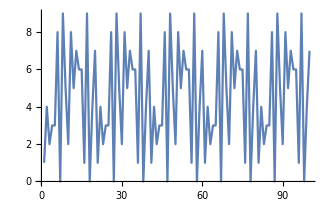
| Expected output: |  
  | -Graphics- |

Join lists of the first 20 squares and cubes, and get the 10 smallest elements of the combined list. »

| Expected output: |  
  | {1,1,4,8,9,16,25,27,36,49} |

Find the positions of the word “software” in the Wikipedia entry for “computers”. »

| Sample expected output: |  
  | {4594,4732,4739,4747,4769,6070,6164,6186,7608,7665,7687} |

Make a histogram of where the letter “e” occurs in the words in WordList[ ]. »

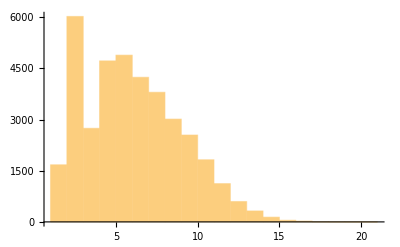
| Expected output: |  
  | -Graphics- |

Make a list of the first 100 cubes, with every one whose position is a square replaced by Red. »

| Expected output: |  
  | {RGBColor[1, 0, 0],8,27,RGBColor[1, 0, 0],125,216,343,512,RGBColor[1, 0, 0],1000,1331,1728,2197,2744,3375,RGBColor[1, 0, 0],4913,5832,6859,8000,9261,10648,12167,13824,RGBColor[1, 0, 0],17576,19683,21952,24389,27000,29791,32768,35937,39304,42875,RGBColor[1, 0, 0],50653,54872,59319,64000,68921,74088,79507,85184,91125,97336,103823,110592,RGBColor[1, 0, 0],125000,132651,140608,148877,157464,166375,175616,185193,195112,205379,216000,226981,238328,250047,RGBColor[1, 0, 0],274625,287496,300763,314432,328509,343000,357911,373248,389017,405224,421875,438976,456533,474552,493039,512000,RGBColor[1, 0, 0],551368,571787,592704,614125,636056,658503,681472,704969,729000,753571,778688,804357,830584,857375,884736,912673,941192,970299,RGBColor[1, 0, 0]} |

Make a list of the first 100 primes, dropping ones whose first digit is less than 5. »

| Expected output: |  
  | {5,7,53,59,61,67,71,73,79,83,89,97,503,509,521,523,541} |

Make a grid starting with Range[10], then at each of 9 steps randomly removing another element. »

| Sample expected output: |  
  | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
1 | 2 | 3 | 5 | 6 | 7 | 8 | 9 | 10 | 
1 | 3 | 5 | 6 | 7 | 8 | 9 | 10 |  | 
3 | 5 | 6 | 7 | 8 | 9 | 10 |  |  | 
3 | 6 | 7 | 8 | 9 | 10 |  |  |  | 
3 | 6 | 7 | 9 | 10 |  |  |  |  | 
3 | 6 | 7 | 9 |  |  |  |  |  | 
6 | 7 | 9 |  |  |  |  |  |  | 
7 | 9 |  |  |  |  |  |  |  | 
9 |  |  |  |  |  |  |  |  |  |

Find the longest 10 words in WordList[ ]. »

| Expected output: |  
  | {"electroencephalographic","electroencephalograph","counterrevolutionary","buckminsterfullerene","compartmentalization","electroencephalogram","internationalization","uncharacteristically","magnetohydrodynamics","incomprehensibility"} |

Find the 5 longest integer names for integers up to 100. »

| Expected output: |  
  | {"seventy-seven","seventy-three","seventy-eight","twenty-three","twenty-eight"} |

Find the 5 English names for integers up to 100 that have the largest number of “e”s in them. »

| Expected output: |  
  | {"seventy-three","seventeen","seventy-seven","nineteen","eleven"} |

Q&A

How does one read list[[n]] out loud?

Usually “list part n” or “list sub n”. The second form (with “sub” short for “subscript”) comes from thinking about math and extracting components of vectors.

What happens if one asks for a part of a list that doesn’t exist?

One gets a message, and the original computation is returned undone.

Can I just get the first position at which something appears in a list?

Yes. Use FirstPosition.

Tech Notes

First and Last are equivalent to [[1]] and [[-1]].

In specifying parts, 1;;-1 is equivalent to All.

More to Explore

Guide to Parts of Lists in the Wolfram Language »